```mathematica
(*** to calculate the unit of rapidity ***)
```

```mathematica
sqrtNN=5020
```

5020

```mathematica
Ebeam=0.5*sqrtNN
Mbeam=0.938
Pbeam=√(Ebeam^2-Mbeam^2)
ybeam=0.5*Log[(Ebeam+Pbeam)/(Ebeam-Pbeam)]
```

2510.

0.938

2510.

8.58519

```mathematica
sigma=1.9
eta0=2.0
```

1.9

2.

```mathematica
sigma=2.5
eta0=1.4
```

2.5

1.4

```mathematica
(*** right-moving direction ***)
```

```mathematica
f1[eta_]:=Exp[-(Abs[eta]-eta0)^2/(2 sigma^2)UnitStep[Abs[eta]-eta0]]*(1+eta/ybeam)*UnitStep[ybeam+eta]
```

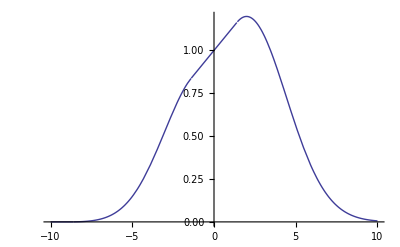

```mathematica
Plot[f1[eta],{eta,-10,10}]
```

```mathematica
NIntegrate[f1[eta],{eta,-10,10}]
```

9.06357

```mathematica
NIntegrate[f1[eta],{eta,-0.5,0.5}]
```

1.

```mathematica
NIntegrate[f1[eta],{eta,-1,1}]
```

2.

```mathematica
$aj
```

```mathematica
NIntegrate[f1[eta],{eta,-2,2}]
```

3.98858

```mathematica
NIntegrate[f1[eta],{eta,-2.4,2.4}]
```

4.74792

```mathematica
NIntegrate[f1[eta],{eta,-3,3}]
```

5.79434

```mathematica
(*** left-moving direction ***)
```

```mathematica
f2[eta_]:=Exp[-(Abs[eta]-eta0)^2/(2 sigma^2)UnitStep[Abs[eta]-eta0]]*(1-eta/ybeam)*UnitStep[ybeam-eta]
```

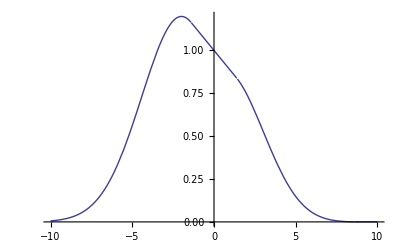

```mathematica
Plot[f2[eta],{eta,-10,10}]
```

```mathematica
NIntegrate[f2[eta],{eta,-10,10}]
```

9.06357

```mathematica
NIntegrate[f2[eta],{eta,-0.5,0.5}]
```

1.

```mathematica
NIntegrate[f2[eta],{eta,-1,1}]
```

2.

```mathematica
NIntegrate[f2[eta],{eta,-2,2}]
```

3.98858

```mathematica
NIntegrate[f2[eta],{eta,-3,3}]
```

5.79434

```mathematica
(*** left & right moving ***)
```

```mathematica
f2[eta_]:=Exp[-(Abs[eta]-eta0)^2/(2 sigma^2)UnitStep[Abs[eta]-eta0]]*UnitStep[ybeam+eta]UnitStep[ybeam-eta]
```

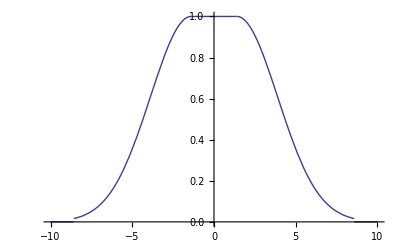

```mathematica
Plot[f2[eta],{eta,-10,10}]
```

```mathematica
NIntegrate[f2[eta],{eta,-10,10}]
```

9.04118

```mathematica
NIntegrate[f2[eta],{eta,-0.5,0.5}]
```

1.

```mathematica
NIntegrate[f2[eta],{eta,-1,1}]
```

2.

```mathematica
NIntegrate[f2[eta],{eta,-2,2}]
```

3.98858

```mathematica
NIntegrate[f2[eta],{eta,-3,3}]
```

5.79434